```mathematica
Clear[h,Δ,ξ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx[kx,ky],by[kx,ky],bz[kx,ky]}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];



Δ[kx_,ky_]=ⅈ Δ0[kx,ky]*PauliMatrix[0]+{Δx[kx,ky],ⅈ Δy[kx,ky],Δz[kx,ky]}.Table[PauliMatrix[i],{i,3}];

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]†,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx[kx,ky]∈Reals,by[kx,ky]∈Reals,bz[kx,ky]∈Reals,kx∈Reals,ky∈Reals}];

(* check if hermitian *)
Print["H is hermitian: "<>ToString[DeleteDuplicates[Flatten[Refine[H[kx,ky]-H[kx,ky]†,{bx[kx,ky]∈Reals,by[kx,ky]∈Reals,bz[kx,ky]∈Reals,kx∈Reals,ky∈Reals}]]]=={0}]]
```

H is hermitian: False

```mathematica
(* check C-symmetry : Subscript[U, c] = Subscript[τ, 1] ⊗ Subscript[σ, 2] *)
UC = KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
FullSimplify[H[kx,ky]+UC.H[kx,ky].UC†,Assumptions->{kx∈Reals,ky∈Reals,ξ[kx,ky]∈Reals,bx[kx,ky]∈Reals,by[kx,ky]∈Reals,bz[kx,ky]∈Reals,
Δ0[kx,ky]∈Reals,Δx[kx,ky]∈Reals,Δy[kx,ky]∈Reals,Δz[kx,ky]∈Reals}]/.{bz[kx,ky]-> 0};
%//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* check P-symmetry : Subscript[U, P] = Subscript[τ, 1] ⊗ Subscript[σ, 3] *)
UP = KroneckerProduct[PauliMatrix[1],PauliMatrix[3]];
FullSimplify[H[kx,ky]+UP.(H[-kx,-ky]* ).UP†/.{bz[kx,ky]-> 0,ξ[-kx,-ky]-> ξ[kx,ky],bz[-kx,-ky]-> 0,bx[-kx,-ky]-> bx[kx,ky],by[-kx,-ky]-> by[kx,ky],
Δ0[-kx,-ky]-> -Δ0[kx,ky],Δz[-kx,-ky]-> -Δz[kx,ky],Δx[-kx,-ky]-> Δx[kx,ky],Δy[-kx,-ky]-> -Δy[kx,ky]},Assumptions->{kx∈Reals,ky∈Reals,ξ[kx,ky]∈Reals,bx[kx,ky]∈Reals,by[kx,ky]∈Reals,bz[kx,ky]∈Reals,ξ[-kx,-ky]∈Reals,bx[-kx,-ky]∈Reals,by[-kx,-ky]∈Reals,bz[-kx,-ky]∈Reals,
Δ0[kx,ky]∈Reals,Δx[kx,ky]∈Reals,Δy[kx,ky]∈Reals,Δz[kx,ky]∈Reals,
Δ0[-kx,-ky]∈Reals,Δx[-kx,-ky]∈Reals,Δy[-kx,-ky]∈Reals,Δz[-kx,-ky]∈Reals}];
%//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(1-Cos[kx]-Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,bz}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(Sin[kx]-ⅈ Sin[ky]);
Δdd[kx_,ky_]=+(Sin[kx]+ⅈ Sin[ky]);
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];

(* check if hermitian *)
Print["H is hermitian: "<>ToString[DeleteDuplicates[Flatten[Refine[H[kx,ky]-H[kx,ky]†,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}]]]=={0}]]
```

H is hermitian: True

```mathematica
H[kx,ky]⟦3;;4,3;;4⟧
```

{{-1-bz+Cos[kx]+Cos[ky],bx+ⅈ by},{bx-ⅈ by,-1+bz+Cos[kx]+Cos[ky]}}

```mathematica
H[-kx,-ky]⟦1;;2,1;;2⟧
```

{{1+bz-Cos[kx]-Cos[ky],bx-ⅈ by},{bx+ⅈ by,1-bz-Cos[kx]-Cos[ky]}}

```mathematica
h[kx,ky] // MatrixForm
```

(1+bz-Cos[kx]-Cos[ky] | bx-ⅈ by
bx+ⅈ by | 1-bz-Cos[kx]-Cos[ky])

```mathematica
(* for the convention of the Hamiltonian above the τ matrix should come first in the Kronecker product *)
KroneckerProduct[{{t11,t12},{t21,t22}},{{s11,s12},{s21,s22}}];
%//MatrixForm
```

(s11 t11 | s12 t11 | s11 t12 | s12 t12
s21 t11 | s22 t11 | s21 t12 | s22 t12
s11 t21 | s12 t21 | s11 t22 | s12 t22
s21 t21 | s22 t21 | s21 t22 | s22 t22)

```mathematica
(* check C-symmetry : Subscript[U, c] = Subscript[τ, 1] ⊗ Subscript[σ, 2] *)
UC = KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
FullSimplify[H[kx,ky]+UC.H[kx,ky].UC†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
(* I guess they assume bz=0 here... *)
```

(2 bz | 0 | 0 | 0
0 | -2 bz | 0 | 0
0 | 0 | -2 bz | 0
0 | 0 | 0 | 2 bz)

```mathematica
(* check P-symmetry : Subscript[U, P] = Subscript[τ, 1] ⊗ Subscript[σ, 3] *)
USig2 = KroneckerProduct[{{1,0},{0,1}},PauliMatrix[2]];
FullSimplify[H[kx,ky]+USig2.(H[kx,ky]).USig2†,Assumptions->{kx∈Reals,ky∈Reals}]/.{bz-> 0};
%//MatrixForm
```

(-2 (-1+Cos[kx]+Cos[ky]) | -2 ⅈ by | -2 ⅈ Sin[ky] | 0
2 ⅈ by | -2 (-1+Cos[kx]+Cos[ky]) | 0 | -2 ⅈ Sin[ky]
2 ⅈ Sin[ky] | 0 | 2 (-1+Cos[kx]+Cos[ky]) | 2 ⅈ by
0 | 2 ⅈ Sin[ky] | -2 ⅈ by | 2 (-1+Cos[kx]+Cos[ky]))

```mathematica
(* check P-symmetry : Subscript[U, P] = Subscript[τ, 1] ⊗ Subscript[σ, 3] *)
UP = KroneckerProduct[PauliMatrix[1],PauliMatrix[3]];
FullSimplify[H[kx,ky]+UP.(H[-kx,-ky]* ).UP†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
(* uhm... this is not zero for almost all in-plane b values??? *)
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
H[kx,ky]//MatrixForm
```

(1+bz-Cos[kx]-Cos[ky] | bx-ⅈ by | Sin[kx]-ⅈ Sin[ky] | sx Cos[kx]+sy Cos[ky]
bx+ⅈ by | 1-bz-Cos[kx]-Cos[ky] | sx Cos[kx]+sy Cos[ky] | -Sin[kx]-ⅈ Sin[ky]
Sin[kx]+ⅈ Sin[ky] | sx Cos[kx]+sy Cos[ky] | -1-bz+Cos[kx]+Cos[ky] | -bx-ⅈ by
sx Cos[kx]+sy Cos[ky] | -Sin[kx]+ⅈ Sin[ky] | -bx+ⅈ by | -1+bz+Cos[kx]+Cos[ky])

```mathematica
UP†//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
FullSimplify[UP.H[kx,ky]*.UP†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}]//MatrixForm
```

(-1-bz+Cos[kx]+Cos[ky] | bx-ⅈ by | Sin[kx]-ⅈ Sin[ky] | -sx Cos[kx]-sy Cos[ky]
bx+ⅈ by | -1+bz+Cos[kx]+Cos[ky] | -sx Cos[kx]-sy Cos[ky] | -Sin[kx]-ⅈ Sin[ky]
Sin[kx]+ⅈ Sin[ky] | -sx Cos[kx]-sy Cos[ky] | 1+bz-Cos[kx]-Cos[ky] | -bx-ⅈ by
-sx Cos[kx]-sy Cos[ky] | -Sin[kx]+ⅈ Sin[ky] | -bx+ⅈ by | 1-bz-Cos[kx]-Cos[ky])

```mathematica
(* check T-symmetry *)
UT = KroneckerProduct[PauliMatrix[0],PauliMatrix[2]]ⅈ;
FullSimplify[H[kx,ky]-UT.(H[-kx,-ky]*).UT†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
(* uhm... this is not zero for almost all in-plane b values??? *)
```

(2 bz | 2 (bx-ⅈ by) | 0 | 2 (sx Cos[kx]+sy Cos[ky])
2 (bx+ⅈ by) | -2 bz | 2 (sx Cos[kx]+sy Cos[ky]) | 0
0 | 2 (sx Cos[kx]+sy Cos[ky]) | -2 bz | 2 (bx+ⅈ by)
2 (sx Cos[kx]+sy Cos[ky]) | 0 | 2 (bx-ⅈ by) | 2 bz)

```mathematica
(* check I-symmetry *)
UT = KroneckerProduct[PauliMatrix[3],PauliMatrix[0]];
FullSimplify[H[kx,ky]-UT.(H[-kx,-ky]).UT†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
(* uhm... this is not zero for almost all in-plane b values??? *)
```

(0 | 0 | 0 | 2 (sx Cos[kx]+sy Cos[ky])
0 | 0 | 2 (sx Cos[kx]+sy Cos[ky]) | 0
0 | 2 (sx Cos[kx]+sy Cos[ky]) | 0 | 0
2 (sx Cos[kx]+sy Cos[ky]) | 0 | 0 | 0)

```mathematica
(* check MY-symmetry *)
UT = KroneckerProduct[PauliMatrix[3],PauliMatrix[2]]ⅈ;
FullSimplify[H[kx,ky]-UT.(H[kx,-ky]).UT†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
(* uhm... this is not zero for almost all in-plane b values??? *)
```

(2 bz | 2 bx | 0 | 0
2 bx | -2 bz | 0 | 0
0 | 0 | -2 bz | 2 bx
0 | 0 | 2 bx | 2 bz)

```mathematica
(* check C-symmetry : Subscript[U, C] = Subscript[τ, 1] ⊗ Subscript[σ, 1] *)
UC = KroneckerProduct[PauliMatrix[1],PauliMatrix[1]];
FullSimplify[H[kx,ky]+UC.H[kx,ky].UC†,Assumptions->{kx∈Reals,ky∈Reals,bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,sz∈Reals}];
%//MatrixForm
(* uhm... this is not zero for almost all in-plane b values??? *)
```

(2 bz | 2 (bx-ⅈ by) | 0 | 2 (sx Cos[kx]+sy Cos[ky])
2 (bx+ⅈ by) | -2 bz | 2 (sx Cos[kx]+sy Cos[ky]) | 0
0 | 2 (sx Cos[kx]+sy Cos[ky]) | -2 bz | 2 (bx+ⅈ by)
2 (sx Cos[kx]+sy Cos[ky]) | 0 | 2 (bx-ⅈ by) | 2 bz)

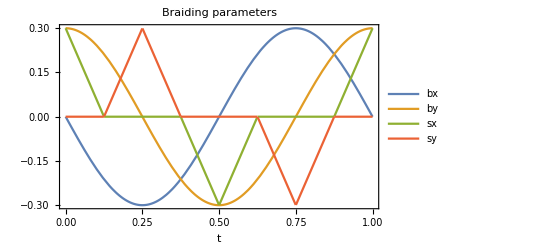

```mathematica
b0=-.3;
s0=+.3;
Bx[t_]:= +b0*Sin[t*2π]
By[t_]:= -b0*Cos[t*2π]
Sx[t_]:=s0*Piecewise[{ {1-1/.125t,0≤t≤.125},{-1/.125(t-.375),.375<t≤.5},{-1+1/.125(t-.5),.5<t≤.625},{+1/.125(t-.875),.875<t≤1}}]
Sy[t_]:=s0*Piecewise[{ {1/.125(t-.125),.125<t≤.25}, {1-1/.125(t-.25),.25<t≤.375}, {-1/.125(t-.625),.625<t≤.75}, {-1+1/.125(t-.75),.75<t≤.875}}]
Plot[{Bx[t],By[t],Sx[t],Sy[t]},{t,0,1},Frame->True,FrameLabel->{"t"},PlotLegends->{"bx","by","sx","sy"},PlotLabel->"Braiding parameters"]
```

```mathematica
Clear[kx,ky,eval]
eval[kx_,ky_]=Eigenvalues[H[kx,ky]];

(* set the system dimensions *)
Lx=Ly=2;
```

```mathematica
spectrum={};
Monitor[
Do[
tp ={};
Do[
AppendTo[tp,Flatten[eval[kx,ky]/.{bx->Bx[t],by->By[t],bz->0.,t0->1.,sx->Sx[t],sy->Sy[t]}]];
,{kx,0,2π-2π/Lx,2π/Lx},{ky,0,2π-2π/Lx,2π/Ly}];
tp =Sort[Flatten[tp]];
If[Length[tp]>40,
AppendTo[spectrum,tp[[Length[tp]/2-20;;Length[tp]/2+21]]];
,
AppendTo[spectrum,tp];
];
,{t,0.,1,.01}]
,t]
```

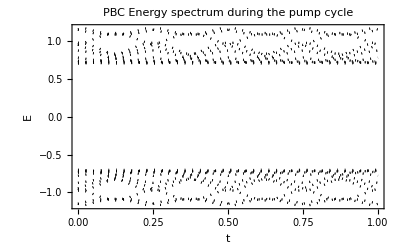

```mathematica
bulk =ListPlot[spectrumᵀ,PlotRange->Full,PlotStyle->Directive[{Black,Dotted}],Joined->True,DataRange->{0,1},Frame->True,FrameLabel->{"t", "E"},PlotLabel->"PBC Energy spectrum during the pump cycle"]
```

```mathematica
(* almost-by-hand FT *)
Clear[δ,Hrs]
(H[kx,ky]*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2]*δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2+1]*δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1+1,x2]*δ[y1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1+1,y2]};
(* assign local real space Hamiltonian *)
Hrs[x1_,x2_,y1_,y2_]=%;
δ[x_,y_]=If[x==y,1,0];

(* now construct the full one *)
Clear[Hfull]
pbc=True;
Hfull= ConstantArray[0,{Lx,Ly,4,Lx,Ly,4}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-2,x2+2},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}]
Hfull=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];

(* diagonalize and plot *)
Clear[t]
specPBC={};
states={};
Monitor[
Do[
{evals,evec}=Eigensystem[N[Hfull/.{bx->Bx[t],by->By[t],bz->0.,t0->-1.,sx->Sx[t],sy->Sy[t]}]];
order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];
If[Length[evals]>40,
AppendTo[specPBC,evals[[Length[evals]/2-20;;Length[evals]/2+21]]];
,
AppendTo[specPBC,evals];
];
(*AppendTo[states,evec];*)
,{t,0.,1,.01}]
,t]
```

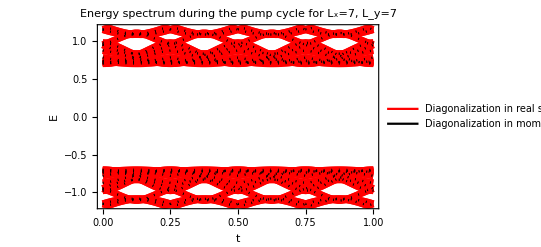

```mathematica
Show[ListPlot[Chop[specPBCᵀ],PlotStyle->Directive[Thickness[.0125],Red],PlotLegends->LineLegend[{Red,Black},{"Diagonalization in real space with PBC", "Diagonalization in momentum space"}],Joined->True,PlotRange->Full,DataRange->{0,1}],bulk,Frame->True,Axes->False,FrameLabel->{"t","E"},PlotLabel->"Energy spectrum during the pump cycle for L_x="<>ToString[Lx]<>", L_y="<>ToString[Ly]]
```

```mathematica
(* now construct the full one *)
Clear[Hfull]
pbc=False; (* this time for OBC!! *)
Hfull= ConstantArray[0,{Lx,Ly,4,Lx,Ly,4}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-1,x2+1},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}]
Hfull=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];

(* diagonalize and plot *)
Clear[t]
specOBC={};
states={};
Monitor[
Do[
{evals,evec}=Eigensystem[N[Hfull/.{bx->Bx[t],by->By[t],bz->0.,t0->-1.,sx->Sx[t],sy->Sy[t]}]];
order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];
If[Length[evals]>40,
AppendTo[specOBC,evals[[Length[evals]/2-20;;Length[evals]/2+21]]];
,
AppendTo[specOBC,evals];
];
(*AppendTo[states,evec];*)
,{t,0.,1,.025}]
,t]
```

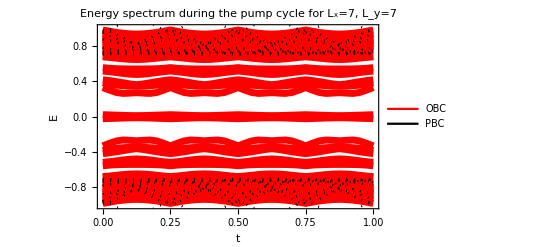

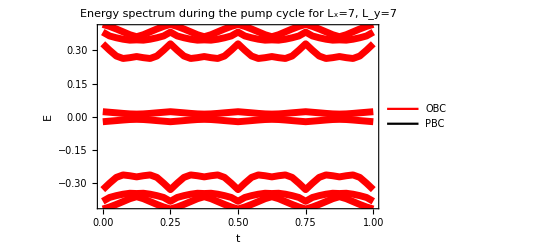

```mathematica
Show[ListPlot[Chop[specOBCᵀ],PlotStyle->Directive[Thickness[.0125],Red],PlotLegends->LineLegend[{Red,Black},{"OBC", "PBC"}],Joined->True,DataRange->{0,1}],bulk,Frame->True,Axes->False,FrameLabel->{"t","E"},PlotLabel->"Energy spectrum during the pump cycle for L_x="<>ToString[Lx]<>", L_y="<>ToString[Ly],PlotRange->{-1,1}]
Show[ListPlot[Chop[specOBCᵀ],PlotStyle->Directive[Thickness[.0125],Red],PlotLegends->LineLegend[{Red,Black},{"OBC", "PBC"}],Joined->True,DataRange->{0,1}],bulk,Frame->True,Axes->False,FrameLabel->{"t","E"},PlotLabel->"Energy spectrum during the pump cycle for L_x="<>ToString[Lx]<>", L_y="<>ToString[Ly],PlotRange->{-1,1}.4]
```